```mathematica
Clear[k12];
Clear[fx1];
Clear[epsn12];
beta=1.0/T;
k12=0.00019714285714285713*T-0.05877814285714285;
k13=0.125205711996-2.9029987*10^(-6)*T;
k23=0.00019714285714285713*T-0.05877814285714285;
dfct1=(1-0.12 Exp[-3. epsn1 beta]);
dfct2=(1-0.12 Exp[-3. epsn2 beta]);
dfct3=(1-0.12 Exp[-3. epsn3 beta]);
fx1=rho1/N1/(rho1/N1+rho2/N2+rho3/N3);
fx2=rho2/N2/(rho1/N1+rho2/N2+rho3/N3);
fx3=rho3/N3/(rho1/N1+rho2/N2+rho3/N3);
ksi0=Pi (rho1+rho2+rho3)/6.0;
ksi1=Pi (rho1 (sig1 dfct1)^(1.0)+rho2 (sig2 dfct2)^(1.0)+rho3 (sig3 dfct3)^(1.0))/6.0;
ksi2=Pi (rho1 (sig1 dfct1)^(2.0)+rho2 (sig2 dfct2)^(2.0)+rho3 (sig3 dfct3)^(2.0))/6.0;
ksi3=Pi (rho1 (sig1 dfct1)^(3.0)+rho2 (sig2 dfct2)^(3.0)+rho3 (sig3 dfct3)^(3.0))/6.0;
sig12=(sig1+sig2)/2.0;
sig13=(sig1+sig3)/2.0;
sig23=(sig2+sig3)/2.0;
Nbar=N1 fx1+N2 fx2+N3 fx3;
epsn12=(1.-k12)*((epsn1 epsn2)^(0.5));
epsn13=(1.-k13)*((epsn1 epsn3)^(0.5));
epsn23=(1.-k23)*((epsn2 epsn3)^(0.5));

fid=rho1 (Log[rho1/N1]-1)/N1+rho2 (Log[rho2/N2]-1)/N2+rho3 (Log[rho3/N3]-1)/N3;
fhs=6.0 ((3.0 ksi1 ksi2)/(1.0-ksi3)+ksi2^3.0/ksi3/((1.0-ksi3)^2.0)+((ksi2^3.0)/(ksi3^2.0)-ksi0) Log[1.0-ksi3])/Pi;
fassoc=-(N1-1.0) rho1 Log[g11]/N1-(N2-1.0) rho2 Log[g22]/N2-(N3-1.0) rho3 Log[g33]/N3;
g11=1.0/(1.0-ksi3)+1.5 ksi2 sig1 dfct1/((1.0-ksi3)^(2.0))+0.5 ((ksi2)^2.0 (sig1^2.0) (dfct1)^2.0)/((1.0-ksi3)^3.0);
g22=1.0/(1.0-ksi3)+1.5 ksi2 sig2 dfct2/((1.0-ksi3)^(2.0))+0.5 ((ksi2)^2.0 (sig2^2.0) (dfct2)^2.0)/((1.0-ksi3)^3.0);
g33=1.0/(1.0-ksi3)+1.5 ksi2 sig3 dfct3/((1.0-ksi3)^(2.0))+0.5 ((ksi2)^2.0 (sig3^2.0) (dfct3)^2.0)/((1.0-ksi3)^3.0);

Mfm1=(1.0+Nbar (8.0 ksi3-2.0 (ksi3^2.0))/((1-ksi3)^4.0)+(1.0-Nbar) (20.0 ksi3-27.0 ksi3^2.0+12 ksi3^3.0-2 ksi3^4.0)/(1.0-ksi3)^(2.)/(2.0-ksi3)^2.)^-1.0;




Remove[J1a];
Remove[J2a];
Clear[aNv]
J1a=ConstantArray[0,{7,3}];
J2a=ConstantArray[0,{7,3}];
aNv={1.0,(Nbar-1.0)/Nbar,(Nbar-1.0) (Nbar-2.0)/(Nbar^2.0)};

J1a[[1,1]]=0.9105631445;
J1a[[1,2]]=-0.3084016918;J1a[[1,3]]=-0.0906148351;
J1a[[2,1]]=0.6361281449;J1a[[2,2]]=0.1860531159;
J1a[[2,3]]=0.4527842806;
J1a[[3,1]]=2.6861347891;J1a[[3,2]]=-2.5030047259;
J1a[[3,3]]=0.5962700728;
J1a[[4,1]]=-26.547362491;J1a[[4,2]]=21.419793629;
J1a[[4,3]]=-1.7241829131;
J1a[[5,1]]=97.759208784;J1a[[5,2]]=-65.255885330;
J1a[[5,3]]=-4.1302112531;
J1a[[6,1]]=-159.59154087;J1a[[6,2]]=83.318680481;
J1a[[6,3]]=13.776631870;
J1a[[7,1]]=91.297774084;J1a[[7,2]]=-33.746922930;
J1a[[7,3]]=-8.6728470368;

J2a[[1,1]]=0.7240946941;
J2a[[1,2]]=-0.5755498075;J2a[[1,3]]=0.0976883116;
J2a[[2,1]]=2.2382791861;J2a[[2,2]]=0.6995095521;
J2a[[2,3]]=-0.2557574982;
J2a[[3,1]]=-4.0025849485;J2a[[3,2]]=3.8925673390;
J2a[[3,3]]=-9.1558561530;
J2a[[4,1]]=-21.003576815;J2a[[4,2]]=-17.215471648;
J2a[[4,3]]=20.642075974;
J2a[[5,1]]=26.855641363;J2a[[5,2]]=192.67226447;
J2a[[5,3]]=-38.804430052;
J2a[[6,1]]=206.55133841;J2a[[6,2]]=-161.82646165;
J2a[[6,3]]=93.626774077;
J2a[[7,1]]=-355.60235612;J2a[[7,2]]=-165.20769346;
J2a[[7,3]]=-29.666905585;

clear[aJ1];
clear[aJ2];
aJ1=J1a.aNv;
aJ2=J2a.aNv;

clear[ksi3lst];
ksi3lst=Array[ksi3^(#-1.0)&,7];
J1=Simplify[aJ1.ksi3lst];
J2=Simplify[aJ2.ksi3lst];
fdisp=-Pi (rho1)^(2.0) (2 J1 beta epsn1+Nbar (Mfm1) J2 (beta epsn1)^2.0) (sig1)^(3.0)-Pi (rho2)^(2.0) (2 J1 beta epsn2+Nbar (Mfm1) J2 (beta epsn2)^2.0) (sig2)^(3.0)-Pi (rho3)^(2.0) (2 J1 beta epsn3+Nbar (Mfm1) J2 (beta epsn3)^2.0) (sig3)^(3.0)-2.0*Pi rho1 rho2 (2 J1 beta epsn12+Nbar (Mfm1) J2 (beta epsn12)^2.0) sig12^(3.0)-2.0*Pi rho1 rho3 (2 J1 beta epsn13+Nbar (Mfm1) J2 (beta epsn13)^2.0) sig13^(3.0)-2.0*Pi rho2 rho3 (2 J1 beta epsn23+Nbar (Mfm1) J2 (beta epsn23)^2.0) sig23^(3.0);

ftt=fdisp+fhs+fassoc;
dfdrho1=D[ftt,rho1];
dfdrho2=D[ftt,rho2];
dfdrho3=D[ftt,rho3];
prstt=(dfdrho1*rho1+dfdrho2*rho2+dfdrho3*rho3-ftt+rho1/N1+rho2/N2+rho3/N3);




NAnum=6.022 (10^-4);
Mco2=22.;
Mpoly=1000./45;
Mcyl=35.25;
asN1=2.0;
assig=2.79;
asepsn1=170.5;
asN2=45;
assig2=1.0769004906526747;
asepsn2=223;
asN3=2.;
assig3=3.923919882/assig;
asepsn3=289.9999604428;
asbeta=1.380649*(10^-23);
prsfct=asbeta 10^24/assig^3;


mu1=(dfdrho1+Log[rho1/N1]/N1)/.{N1->asN1,sig1->1.0,epsn1->asepsn1,N2->asN2,sig2->assig2,epsn2->asepsn2,N3->asN3,sig3->assig3,epsn3->asepsn3};
mu2=(dfdrho2+Log[rho2/N2]/N2)/.{N1->asN1,sig1->1.0,epsn1->asepsn1,N2->asN2,sig2->assig2,epsn2->asepsn2,N3->asN3,sig3->assig3,epsn3->asepsn3};
mu3=(dfdrho3+Log[rho3/N3]/N3)/.{N1->asN1,sig1->1.0,epsn1->asepsn1,N2->asN2,sig2->assig2,epsn2->asepsn2,N3->asN3,sig3->assig3,epsn3->asepsn3};
prsttasg=prstt/.{N1->asN1,sig1->1.0,epsn1->asepsn1,N2->asN2,sig2->assig2,epsn2->asepsn2,N3->asN3,sig3->assig3,epsn3->asepsn3};


fmu1[rho1_,rho2_,rho3_,T_]:=Evaluate[mu1];
fmu2[rho1_,rho2_,rho3_,T_]:=Evaluate[mu2];
fmu3[rho1_,rho2_,rho3_,T_]:=Evaluate[mu3];
fprsttasg[rho1_,rho2_,rho3_,T_]:=Evaluate[prsttasg];
```

```mathematica
fprsttasg[0.4,0,0,290]/(1.38065*^-23*290)/(2.79*^-10)^3*0.044/6.022*^23/1*^6
```

1.60535×10^16

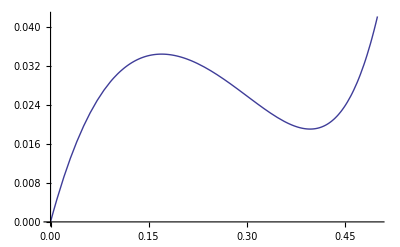

```mathematica
Plot[fprsttasg[ρco2,0,0,290],{ρco2,0,0.5}]
```